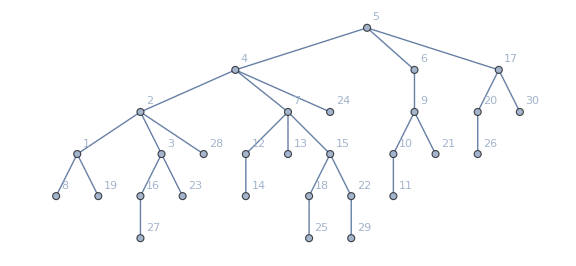

```mathematica
(*Function to generate a tree-like graph*)generateTreeGraph[vertexCount_]:=Module[{edges={},i},(*Generate a simple tree structure*)For[i=2,i<=vertexCount,i++,AppendTo[edges,{i,RandomInteger[{1,i-1}]}];];
(*Create graph*)Graph[Range[vertexCount],UndirectedEdge@@@edges,VertexLabels->"Name",ImageSize->Large]]

(*Depth-first search (DFS) with step storage*)
depthFirstSearch[graph_,startVertex_]:=Module[{visited={},stack,steps={},currentVertex,neighbors},stack={startVertex};(*Stack for DFS*)While[Length[stack]>0,(*Pop vertex from stack*)currentVertex=Last[stack];
stack=Most[stack];
If[!MemberQ[visited,currentVertex],AppendTo[visited,currentVertex];(*Mark as visited*)(*Store step:{current vertex,neighbors being explored}*)neighbors=Complement[VertexList[NeighborhoodGraph[graph,{currentVertex},1]],visited];
AppendTo[steps,{currentVertex,neighbors}];
stack=Join[stack,Reverse[neighbors]]; (*Reverse for DFS order*)]];
steps]

(*Breadth-first search (BFS) with step storage*)
breadthFirstSearch[graph_,startVertex_]:=Module[{visited={},queue,steps={},currentVertex,neighbors},queue={startVertex};(*Queue for BFS*)While[Length[queue]>0,(*Dequeue vertex*)currentVertex=First[queue];
queue=Rest[queue];
If[!MemberQ[visited,currentVertex],AppendTo[visited,currentVertex];(*Mark as visited*)(*Store step:{current vertex,neighbors being explored}*)neighbors=Complement[VertexList[NeighborhoodGraph[graph,{currentVertex},1]],visited];
AppendTo[steps,{currentVertex,neighbors}];
queue=Join[queue,neighbors]; (*Add to queue for BFS order*)]];
steps]

(*Function to display final result or walk through steps*)
showSteps[graph_,steps_,finalOrStepByStep_]:=Module[{currentStep,graphCell=None,highlightedGraph,finalGraph},
If[finalOrStepByStep===vysledok,
Do[
Print["Step: ",steps[[i,1]]," Neighbors: ",steps[[i,2]]];
,{i,1,Length[steps]}
];
,
If[finalOrStepByStep===postup,
For[i=1,i<=Length[steps],i++,
currentStep=steps[[i]];
Do[
highlightedGraph=HighlightGraph[graph,Style[UndirectedEdge[currentStep[[1]],neighbor],Thick,Red]];
finalGraph=highlightedGraph;
If[graphCell=!=None,NotebookDelete[graphCell]];
graphCell=PrintTemporary[finalGraph];
InputString["Press ENTER to continue..."];
,{neighbor,currentStep[[2]]}]; 
];
]
]
]

(*Main program*)
Module[{vertexCount,searchType,treeGraph,startVertex,steps,inputType},(*Get the number of vertices from the user*)vertexCount=Input["Enter the number of vertices: "];
(*Generate tree graph*)treeGraph=generateTreeGraph[vertexCount];
Print[treeGraph];(*Show graph*)(*Get the search type from the user*)searchType=Input["Enter 'depth' for Depth-First Search or 'width' for Breadth-First Search: "];
(*Get the start vertex*)startVertex=Input["Enter the start vertex: "];
(*Perform the selected search*)steps=If[searchType===depth,depthFirstSearch[treeGraph,startVertex],If[searchType===width,breadthFirstSearch[treeGraph,startVertex],Print["Invalid search type!"]]];
(*Wait for user input to display the result or step-by-step process*)
inputType=Input["Enter 'vysledok' for final result or 'postup' for step-by-step: "];
showSteps[treeGraph,steps,inputType];]
```